# Visualising a Binary Black Hole Merger

Macy Maurer Levin

Katja Della Libera and Jonathan Gorard

#### Introduction

On September 14th, 2015, LIGO (the Laser Interferometer Gravitational-Wave Observatory), located in both Washington and Louisiana, detected a strange “ping” roughly 1.3 billion light years away from Earth. This “ping” was caused by gravitational waves as the result of a collision of two black holes which occurred 1.3 billion years ago just as Earth’s inner core began to form. The purpose of this project was to visualise the relationship of a binary black hole system and the eventual collision which marked a revolutionary event in the history of astrophysics.

#### Developing the Visualisation

In order to develop the visualisation, a set of differential equations had to be solved. Respectively, each equation modeled the average angular momentum magnitude along the Z-axis (seeing as the final result was to be three-dimensional), the rate of change of the semi-major axis, the eccentricity, the radius, and the angular velocity about the centre of inertia for the black holes--the result of which is show here:

A function of eccentricity:

```mathematica
e[t_]:=√(1-((m+1)*(L[t])^2)/(m^2*a[t]))
```

```mathematica
m=1.1
```

1.1

Average angular momentum magnitude along the Z-axis and the rate of change of the semi-major axis :

```mathematica
system1=NDSolve[{L'[t]==-((32 1^(7/2)m^2(1+m)^(1/2))/(5 1^5 a[t]^(7/2)))(1/(1-e[t]^2)^2)(1+(7/8)e[t]^2), 
a'[t]==-(2 m^8 a[t]^(1/2))/(15(1+m)^(5/2)L[t]^7)(435-366((m+1)L[t]^2)/(m^2 a[t])+37((1+m)^2 L[t]^4)/(m^4 a[t]^2)),L[0]==4,a[0]==100},{L,a},{t,0,10000}]
```

{{L→InterpolatingFunction[…],a→InterpolatingFunction[…]}}

```mathematica
angularMomentum[t_]:=L[t]/.system1[[1]]
```

```mathematica
semiMajorAxis[t_]:=a[t]/.system1[[1]]
```

```mathematica
angularMomentum[1]
```

3.99998

```mathematica
semiMajorAxis[1]
```

99.9908

```mathematica
(a[t]/.system1)
```

{InterpolatingFunction[…][t]}

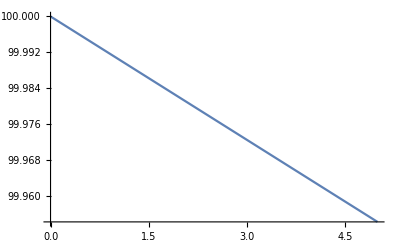

```mathematica
Plot[Evaluate[a[t]/.system1],{t,0,5}]
```

```mathematica
eccentricity[t_]:=√(1-((m+1)*(angularMomentum[t])^2)/(m^2*semiMajorAxis[t]))
```

Radius:

```mathematica
r[t_]:=(semiMajorAxis[t]*(1-(eccentricity[t])^2))/(1+eccentricity[t]Cos[θ[t]])
```

Angular velocity about the center of inertia:

```mathematica
θ[t_]:=θ'[t]==√((1(1+m)a[t](1-e[t]^2))/r[t]^2)
```

```mathematica
system3=NDSolve[{θ'[t]==√((1(1+m)*semiMajorAxis[t]*(1-eccentricity[t]^2))/r[t]^2),θ[0]==0},θ,{t,0,10000}]
```

After evaluating the differential equations, graphs could be determined from which the points representing the black holes could be plotted, a place from which the final visualization could be created. Initially, two rotating points were created using an animation on a circular plot orbiting parallel to each other around the center of mass, also known as a “barycenter”:

```mathematica
Animate[Show[{ContourPlot[x^2+1 y^2==3,{x,-2,2},{y,-2,2}],Graphics[{RGBColor[0,0,0],Disk[{Sqrt[3] Sin[x],Sqrt[3] Cos[x]},0.1]},PlotRange->{{-2,2},{-2,2}}], Graphics[{RGBColor[0,0,0],Disk[{Sqrt[3] Sin[(x+3)],Sqrt[3] Cos[(x+3)]},0.1]},PlotRange->{{-2,2},{-2,2}}]}],{x,0,2 Pi,0.01},SaveDefinitions->"True"]
```

Once this simple animation and the graphs were complete, the two were merged by a common function which allowed for the points plotted on the first animation to follow the path of the spiral graphs developed from the various initial conditions provided alongside the differential equations. Initially, the animation was developed via a function where one of the black holes remained stationary whilst the other one orbited around it following the path of the graph, gradually getting closer and closer as the distance decreased but the acceleration increased, a relationship modeled by the proportionality: ∆r∝∆t.

```mathematica
simulatePath2[mass_,initialsemimajoraxis_,initialangularmomentum_,maxtime_,mintime_:0,animationrate_:5]:=
	Module[{e,m,L,a,system1,angularMomentum,semiMajorAxis,eccentricity,
		r,θ,system2,angle,radius,seed,n1,n2,tinystars,smallstars,x},
	e[t_]:=√(1-((m+1)*(L[t])^2)/(m^2*a[t]));
	m=mass;
	system1=NDSolve[{L'[t]==-((32 1^(7/2)m^2(1+m)^(1/2))/(5 1^5 a[t]^(7/2)))(1/(1-e[t]^2)^2)(1+(7/8)e[t]^2), 
		a'[t]==-(2 m^8 a[t]^(1/2))/(15(1+m)^(5/2)L[t]^7)(435-366((m+1)L[t]^2)/(m^2 a[t])+37((1+m)^2 L[t]^4)/(m^4 a[t]^2)),
		L[0]==initialangularmomentum,
		a[0]==initialsemimajoraxis},{L,a},{t,0,maxtime}];
	angularMomentum[t_]:=L[t]/.system1[[1]];
	semiMajorAxis[t_]:=a[t]/.system1[[1]];
	eccentricity[t_]:=√(1-((m+1)*(angularMomentum[t])^2)/(m^2*semiMajorAxis[t]));
	r[t_]:=(semiMajorAxis[t]*(1-(eccentricity[t])^2))/(1+eccentricity[t]Cos[θ[t]]);
	system2=NDSolve[{θ'[t]==√((1(1+m)*semiMajorAxis[t]*(1-eccentricity[t]^2))/r[t]^2),θ[0]==0},θ,{t,0,maxtime}];
	angle[x_]:=Re[θ[x]/.system2[[1]]];
	radius[x_]:=Re[(semiMajorAxis[x]*(1-(eccentricity[x])^2))/(1+eccentricity[x]Cos[angle[x]])];
	tinystars= 50 Table[{Cos[#1]Sqrt[1-#2^2],Sin[#1]Sqrt[1-#2^2],#2}&[RandomReal[{0,2Pi}],RandomReal[{-1,1}]],{5000}];
	smallstars= 45 Table[{Cos[#1]Sqrt[1-#2^2],Sin[#1]Sqrt[1-#2^2],#2}&[RandomReal[{0,2Pi}],RandomReal[{-1,1}]],{500}];
		
	Row[{Plot[radius[t],{t,mintime,maxtime},PlotPoints->1000,AxesLabel->{"time","radius"},
			ImageSize->{450,400}],
	
	Animate[Show[
		ParametricPlot3D[{(1-m/(1+m)){radius[t] Cos[angle[t]], 
			radius[t]Sin[angle[t]],0},(m/(1+m)){-radius[t] Cos[angle[t]],-radius[t] Sin[angle[t]],0}},
			{t,mintime,maxtime},PlotPoints->5000],
		Graphics3D[{RGBColor[0,0,0],Sphere[(1-m/(1+m)){radius[x] Cos[angle[x]],radius[x] Sin[angle[x]],0}]}], 
		Graphics3D[{RGBColor[0,0,0],Sphere[(m/(1+m)){-radius[x] Cos[angle[x]],-radius[x] Sin[angle[x]],0}]}],
			ImageSize->{450,400},
			PlotRange->{Max[{(1-m/(1+m)),(m/(1+m))}]{-radius[mintime] ,radius[mintime] },
				Max[{(1-m/(1+m)),(m/(1+m))}]{-radius[mintime] ,radius[mintime] },
				{-2,2}}],
		{{x,mintime,"time"},mintime,maxtime},
		SaveDefinitions->True,
		AnimationRate->animationrate],
	Animate[Show[
			Graphics3D[{
				RGBColor[1,1,1],PointSize[0.003],Point[tinystars],
				RGBColor[1,1,1],PointSize[0.006],Point[smallstars]}],
			Graphics3D[{RGBColor[0,0,0],Sphere[(1-m/(1+m)){radius[x] Cos[angle[x]],radius[x] Sin[angle[x]],0}]}], 
			Graphics3D[{RGBColor[0,0,0],Sphere[(m/(1+m)){-radius[x] Cos[angle[x]],-radius[x] Sin[angle[x]],0}]}],
			Background->RGBColor[0.07,0.2,0.40],Boxed->False,SphericalRegion->True,
				ImageSize->{450,400},Lighting->Automatic,ViewVector->{0,0,-20},ViewAngle->60°],
		{{x,mintime,"time"},mintime,maxtime},
		SaveDefinitions->True,
		AnimationRate->animationrate]}]]
```

For the final animation, a star-field was created which served as the background for the polished visualization (the color of “space” was changed to a dark blue in order to see the orbit of the black holes).

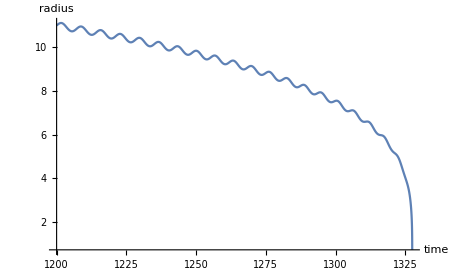

```mathematica
simulatePath2[1.1,20,3.39,1327.49,1200,4]
```

#### Conclusion

In conclusion, this demonstration was able to successfully visualize a binary black hole merger as discovered by LIGO, and as predicted by Albert Einstein’s General Theory of Relativity in 1916. Through this visualization, thought it is somewhat simple, we can view this incredible phenomenon, and are given a glimpse as to what it may be like if we could see the real event with our own eyes. In the future, a second part of the project would be added to determine the distance of the gravitational wave detector from the black holes, and the time the signal reached the detector .